This code is released under the GPL license. Copyright 2018 by Valerio Marra (valerio.marra@me.com)

## Preamble

```mathematica
ClearAll["Global`*"];
$VersionNumber
SetDirectory[NotebookDirectory[]];
accugoal=8;
Get["code-stat/Ltools.m"];
Get["code-stat/triplotF.m"];
Get["code-stat/triplotP.m"];
Get["code-stat/triplotPser.m"];
Get["code-stat/triplotCombo.m"];
```

11.3

Get::noopen: Cannot open code-stat/triplotPser.m.

```mathematica
maxMemAllowed=0.8 $SystemMemory;  (* 80% of your RAM *)
Print[Row[{"Max memory allowed: ",Round[maxMemAllowed/1024^3,.1]," GB"}]];
intervalBetweenTests=1;(*seconds*)
iAmAliveSignal=0;
Dynamic[iAmAliveSignal];
RunScheduledTask[
	If[MemoryInUse[]>maxMemAllowed,Print["..quitting Mathematica, too much RAM used :S"];Quit[],iAmAliveSignal++]
,intervalBetweenTests];
```

Max memory allowed: 51.2 GB

```mathematica
(* Removes memory limit below if needed *)
(*RemoveScheduledTask[ScheduledTasks[]];*)
```

## Intro

```mathematica
(* choose the color scheme (1 to 5); 0 to display the available colors *)
cs=1;
showpal;Print[palette];
```

-Graphics-

### Loading the table

```mathematica
(* put the appropriate rname and run values and run everything *)
rname="JLA";
run=1;
Get[ToFileName["results-chi2",rname<>"_run"<>ToString[run]<>"-log.txt"]]

actgrid=Flatten[Position[pSet[[All,3]],n_ /; n!=1]];
pSet=pSet[[actgrid]];
pMin=pSet[[All,1]];pMax=pSet[[All,2]];
ngrid=pSet[[All,3]];
pardim=Length[actgrid];
parnames=parnames[[actgrid]];
TableForm[pSet,TableHeadings->{parnames,{"min","max","grid"}}]

AbsoluteTiming[aux=Import[ToFileName["results-chi2",rname<>"_run"<>ToString[run]<>".r32"],"Real32"];]
AbsoluteTiming[
chi2TabPar=ArrayReshape[aux,Join[ngrid,{1}]];
ParSpaceTab=pTabX[#,pMin,pMax,ngrid]& /@Range[pardim];
aux2=Map[(#)&,Tuples[ParSpaceTab]];
aux2=N@Flatten[aux2];
aux2=ArrayReshape[aux2,Join[ngrid,{Length[aux2]/(Times@@ngrid)}]];
chi2TabPar=Join[aux2,chi2TabPar,Length[Dimensions[aux2]]];
]
ClearAll[ParSpaceTab,aux2];

Needs["Developer`"];
If[PackedArrayQ[chi2TabPar],Null,chi2TabPar=ToPackedArray[chi2TabPar];];
Row[{ByteCount[chi2TabPar]/1024^2.,"MB"}]
PackedArrayForm[chi2TabPar]
(*On["Packing"];*)
```

Calculation ended on Thu 10 May 2018 10:18:44  -  0.h or 0.9m of total computation  -  0.00082s per grid point

| min | max | grid
Ω_m | 0.1 | 0.5 | 40
w_0 | -1.4 | -0.6 | 40
w_a | -1 | 1 | 40

{0.049247,Null}

{0.064356,Null}

1.95329MB

PackedArray[Real,<40,40,40,4>]

### Best fit model

```mathematica
AbsoluteTiming[Dimensions[auxtab=Flatten[chi2TabPar,pardim-1]]]
(*AbsoluteTiming[Dimensions[auxtabchi2=auxtab[[All,pardim+1]]];]
AbsoluteTiming[supermin=Min[auxtabchi2];]
AbsoluteTiming[superpos=Position[auxtabchi2,supermin][[1]];]
AbsoluteTiming[superposc=auxtab[[superpos]][[1]];]*)
spos=SparseArray[Unitize[#],Automatic,1]["AdjacencyLists"]&;
AbsoluteTiming[supers=auxtab[[spos[#-Min@#]]]&@aux]
superposc=Mean[supers];Column[{""}]

skipEvi=0;
If[skipEvi==0,Etemp=AbsoluteTiming[EVI=evidence[chi2TabPar];][[1]];]
Row[{"Assuming χ^2 = -2 Log[prior*likelihood], the evidence E is: Log E=",EVI,"  -  it took: ",Round[Etemp,.1],"s"}]
If[useFisher==1,
Print[Row[{"Fisher evidence: Log E=",logFEvi}]];
Print[Row[{"Numeric evidence: Log E=",logNEvi,"  -  limiting the integration within the n-σ Fisher ellipsoid"}]];]
tabbf=If[VectorQ[vecF],
{Join[parnames,{"χ^2"}],superposc,Join[vecF,{chi2minfi}],Thread[Abs[superposc[[;;-2]]-vecF]≤(pMax-pMin)/(ngrid-1)],Round[Abs[superposc[[;;-2]]-vecF]/((pMax-pMin)/(ngrid-1)),.01]}
,{Join[parnames,{"χ^2"}],superposc}];
TableForm[tabbf,TableHeadings->{{"","Grid","FindMinimum","Within grid step?","# of steps"},{"Best-fit","model"}}]
Export[ToFileName["results-analysis",rname<>"-run"<>ToString[run]<>"-best_fit.txt"],superposc,"Table","TableHeadings"->{Join[parnames,{"\!\(\*SuperscriptBox[\(χ\), \(2\)]\)"}]}]
```

{0.001046,{64000,4}}

{0.000729,{{0.315385,-1.03077,-0.179487,25.8541}}}

Assuming χ^2 = -2 Log[prior*likelihood], the evidence E is: Log E=-18.4165  -  it took: 0.s

Fisher evidence: Log E=-18.4461

Numeric evidence: Log E=-18.466  -  limiting the integration within the n-σ Fisher ellipsoid

| Best-fit | model |  | 
 | Ω_m | w_0 | w_a | χ^2
Grid | 0.315385 | -1.03077 | -0.179487 | 25.8541
FindMinimum | 0.319906 | -1.03831 | -0.189026 | 25.8339
Within grid step? | True | True | True | 
# of steps | 0.44 | 0.37 | 0.19 |

results-analysis/JLA-run1-best_fit.txt

```mathematica
ClearAll[aux];
AbsoluteTiming[Share[];]
```

{0.236736,Null}

## 1d posterior

```mathematica
plotname=1; (* choose the variable *)
If[
pardim>1
,
Dimensions[chi2Tab=marginalizeTab[{plotname},chi2TabPar]]
,
plotname=1;
chi2Tab=chi2TabPar[[All,{plotname,-1}]];
Dimensions[chi2Tab]
]
parnames[[plotname]]
```

{40,2}

Ω_m

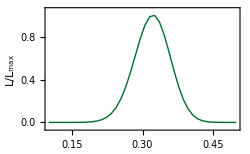

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

| Ω_m | σ^- | σ^+ | x_left | x_right | gau Δχ^2 | actual Δχ^2 | check
1σ | 0.322262 | -0.038837 | 0.0375082 | 0.283425 | 0.35977 | 1 | 1.00501 | 0
2σ | 0.322262 | -0.0795262 | 0.0741628 | 0.242736 | 0.396425 | 4 | 4.04381 | 0
3σ | 0.322262 | -0.12269 | 0.110354 | 0.199572 | 0.432616 | 9 | 9.10717 | 0
4σ | 0.322262 | -0.168908 | 0.146341 | 0.153354 | 0.468603 | 16 | 16.1731 | 0
5σ | 0.322262 | -0.210974 | 0.176876 | 0.111288 | 0.499138 | 25 | 23.708 | 0

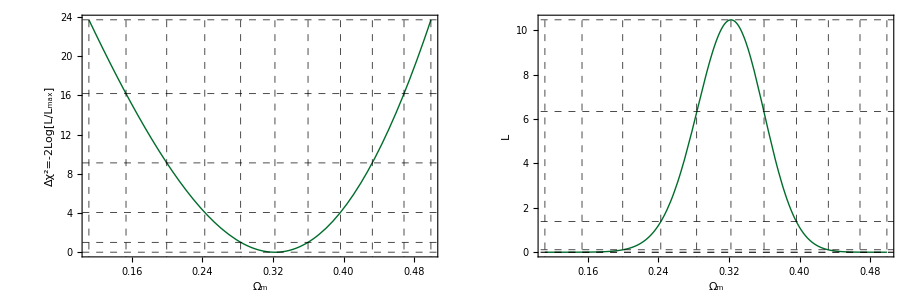

```mathematica
plot1d[chi2Tab,parnames[[plotname]],1];
(*GraphicsRow[{pchisq,plike},ImageSize->800]*)
Show[plike,ImageSize->250]

isig=5;(* -n for n-sigma gaussian levels, n for n-sigma integrated levels; max n=5; 0 to skip levels *)
chi2IO=2; (* interpolation order for chi2; 2 should be used unless the resolution is low and spourious features appear; in this case use 1 *)
method=2; (* method for calculating the sigmas; 2 should be better than 1 *)
noisy=0; (* only for method 2 *)
testlev=1; (* 1 to troubleshoot the likelihood integration, only for method 2 *)

Get["code-stat/c-levels.m"];
clev;

summary=1; (* 1 to print a summary table *)
expout=0; (* 0 not to export output, 1 to export it; includes an interpolating function for the posterior *)
Get["code-stat/f-levels.m"];
Print[plotx];
```

## 2d posterior

```mathematica
plotnames={1,2};(* choose the variables *)
parnames[[plotnames]]
If[
pardim>2
,
Dimensions[chi2Tab=marginalizeTab[plotnames,chi2TabPar]]
,
chi2Tab=Transpose[chi2TabPar,Join[plotnames,{3}]];
chi2Tab[[All,All,{1,2,3}]]=chi2Tab[[All,All,Join[plotnames,{3}]]];
Dimensions[chi2Tab]
]
```

{Ω_m,w_0}

{40,40,3}

| x=Ω_m | y=w_0 | Gaussian levels | Actual levels | error
1σ | 0.315385 | -1.03077 | 2.29575 | 2.27348 | 0
2σ | 0.315385 | -1.03077 | 6.18007 | 6.15376 | 0
3σ | 0.315385 | -1.03077 | 11.8292 | 11.7497 | 0

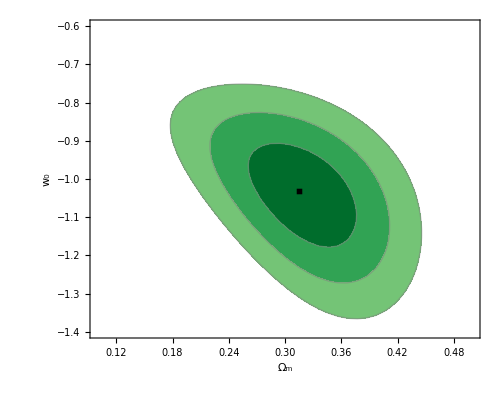

```mathematica
nlevel=3; (* -n for n-sigma gaussian levels, n for n-sigma integrated levels; max n=5 *)
Get["code-stat/a-levels.m"];
testlev=0; (* 1 to troubleshoot the likelihood integration *)
summary=1; (* 1 to print a summary table *)
blev;

plot2dx=ListContourPlot[dchi2TabF,Contours->levels,FrameLabel->parnames[[plotnames]],FrameStyle->20,ContourShading->colorsx[nlevel],ContourStyle->Gray,InterpolationOrder->1,Epilog->Inset[Graphics[{Black,Rectangle[]}],posc,Center,Scaled[.03]],PlotRange->All,AspectRatio->.8,ImageSize->500,Axes->False]
```

```mathematica
(*Export[ToFileName["results-analysis",rname<>"-run"<>ToString[run]<>"-plot2d-par"<>ToString[plotnames[[1]]]<>ToString[plotnames[[2]]]<>".png"],plot2dx,ImageResolution->110]*)
```

```mathematica
(*Export[ToFileName["results-analysis",rname<>"-run"<>ToString[run]<>"-plot2d-par"<>ToString[plotnames[[1]]]<>ToString[plotnames[[2]]]<>".pdf"],plot2dx,"AllowRasterization"->True,ImageResolution->110]*)
```

## TriPlot

{1.19369,Null}

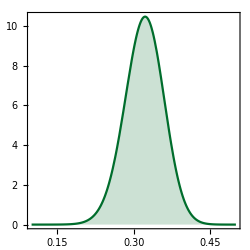
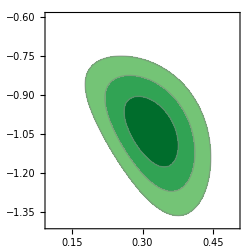
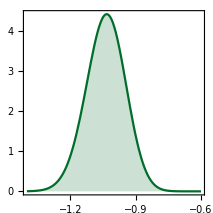
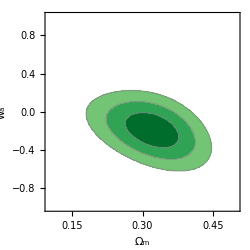
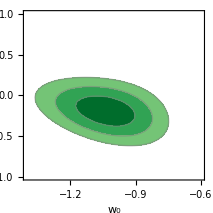
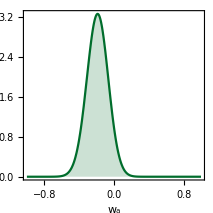
-Graphics- |  | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
triplotkernels=1; (* 1 for serial computation, 0 for as much subkernels as needed, your number *)
(* !!carefull that parallel computation could use a lot of memory!! *)

(*TriPlotP[tlabel_,tab_,parlabels_,nlevelx_,style1d_,style2d_]*)
AbsoluteTiming[triplot=TriPlotP[0,chi2TabPar,parnames,3,{Axis,color1},{colorsx[3],Gray}];]
triplot
```

```mathematica
(*Export[ToFileName["results-analysis",rname<>"-run"<>ToString[run]<>"-triplot.png"],triplot,ImageResolution->400]*)
```

```mathematica
Export[ToFileName["results-analysis",rname<>"-run"<>ToString[run]<>"-triplot.pdf"],triplot,"AllowRasterization"->True,ImageResolution->400]
```

results-analysis/JLA-run1-triplot.pdf

```mathematica
(*TriPlotP[1,chi2TabPar,parnames,3,{None,{color1,Dashed}},{None,{{color1,Dashed}}}]*)
```

## TriPlot with Fisher & Prior

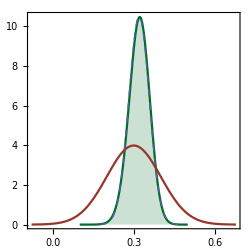
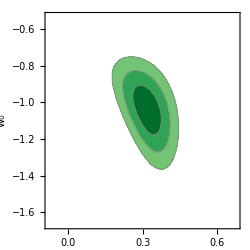
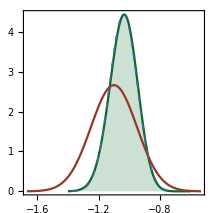
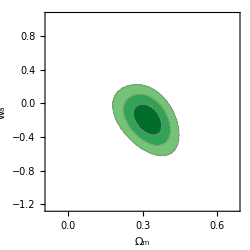
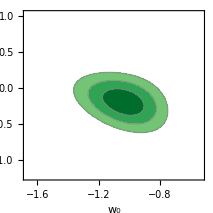
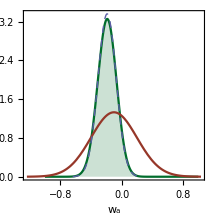
-Graphics- |  | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
Which[
mvprior==1&&useFisher==1&&comboLP==1
,
TriPlotF[1,0,CPMat,vecP,parnames,3,{Darker[TangerineTango]}];
TriPlotF[3,0,CFMat,vecF,parnames,3,{Thick,Dashed,Iris}];
Print[triplotAll=TriPlotCombo[{0,1,3}]];
,
mvprior==1&&useFisher==1
,
TriPlotF[1,0,CPMat,vecP,parnames,3,{Darker[TangerineTango]}];
TriPlotF[2,0,CLMat,vecL,parnames,3,{Darker[Emerald]}];
TriPlotF[3,0,CFMat,vecF,parnames,3,{Thick,Dashed,Iris}];
Print[triplotAll=TriPlotCombo[{0,1,2,3}]];
,
useFisher==1
,
TriPlotF[3,0,CLMat,vecL,parnames,3,{Darker[Emerald]}];
Print[triplotAll=TriPlotCombo[{0,3}]];
];
```

```mathematica
Export[ToFileName["results-analysis",rname<>"-run"<>ToString[run]<>"-triplot_all.pdf"],triplotAll,"AllowRasterization"->True,ImageResolution->400]
```

results-analysis/JLA-run1-triplot_all.pdf

## Combining TriPlots

```mathematica
(*Print[triplots=TriPlotCombo[{0,3}]];*)
```

```mathematica
(*Export[ToFileName["results-analysis",rname<>"-run"<>ToString[run]<>"-triplots.pdf"],triplots,"AllowRasterization"->True,ImageResolution->400]*)
```